```mathematica
5(a)Find  the sum of fourth power of roots of the equation x^4-x^3-7x^2+x+6=0
```

```mathematica
p1=-1;p2=-7;p3=1;p4=6;
Solve[s1+p1==0,s1]
```

{{s1→1}}

```mathematica
Solve[s2+p1*s1+2*p2==0]/.s1->1
```

{{s2→15}}

```mathematica
Solve[s3+p1*s2+p2*s1+3*p3==0,s3]/.{s1->1,s2->15}
```

{{s3→19}}

```mathematica
5(b)equation=DSolve[{y''[t]+y[t]==1,y[0]==0,y[1]==0},y[t],t]
```

{{y[t]→1-Cos[t]+Cot[1] Sin[t]-Csc[1] Sin[t]}}

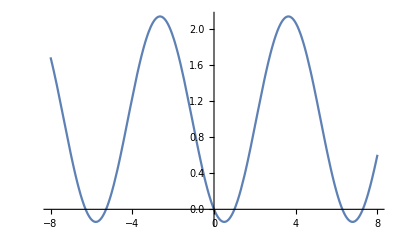

```mathematica
Plot[y[t]/.equation,{t,-8,8}]
```

```mathematica
6(b)sol=
Solve[{x^2+y^2+19 x+4 y-3==0,3 x+4 y==1},{x,y}]//N
m1=sol[[1,2,2]]/sol[[1,1,2]]
```

{{x→-10.1225,y→7.84187},{x→0.122499,y→0.158125}}

-0.774697

```mathematica
m2=sol[[2,2,2]]/sol[[2,1,2]]
```

1.29083

```mathematica
angle=ArcTan[(m1-m2)/(1+m1 m2)]
```

1.5708

```mathematica
angle==90Degree
```

True

```mathematica
ContourPlot[{x^2+y^2+19x+4 y-3==0,3x+4y-1==0},{x,-20,20},{y,-20,20}];
```

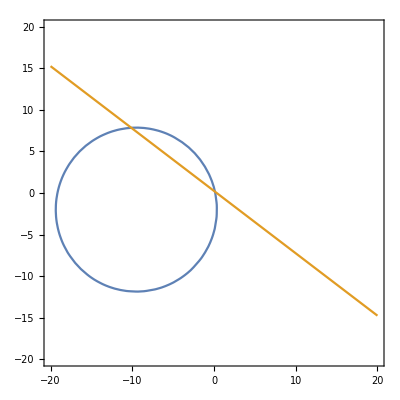

```mathematica
%50
```

```mathematica
%47
```